# Лабораторная работа №6

## Глёза Егор, группа 221701, вариант 2

### Задание 1

Решить задачу Коши для дифференциального уравнения первого порядка на отрезке :
	а) методом Эйлера-Коши с шагом  и , построить графики полученных решений;
	б) методом Рунге-Кутта 4-го порядка с шагом  и , построить графики полученных решений;
	в) с помощью функций DSolve и NDSolve, построить графики.
Сравнить все полученные решения. Сделать выводы о точности методов в зависимости от шага сетки.

Зададим функцию, начальное условие и границы отрезка:

```mathematica
f[x_, y_]:=2x y+0.1 x^2;
y0=0.8;
a=0;
b=1;
```

#### Метод Эйлера-Коши

Зададим функцию для метода Эйлера-Коши:

```mathematica
EulerCouchy[f_,a_,b_,y0_,h_]:=Module[{i,predictor, x,y,n},
n=(b-a)/h;
Array[y,0,n];
x[i_]:=a+i h;
y[0]=y0;
For[i=0,i<n,i++,
predictor= y[i]+h f[x[i],y[i]];
y[i+1]=y[i]+h/2(f[x[i],y[i]+f[x[i+1],predictor]]);
] ;
Table[{x[i],y[i]},{i,0,n-1}]
];
```

#### Метод Рунге-Кутта

Зададим функцию для метода Рунге-Кутта:

```mathematica
RungeKutta4[f_,a_,b_,y0_,h_]:=Module[{i,k1,k2,k3,k4, x,y,n},
n=(b-a)/h;
Array[y,0,n];
y[0]=y0;
x[i_]:=a+i h;
For[i=0,i<n,i++,
k1=h f[x[i],y[i]];
k2=h f[x[i]+h/2,y[i]+k1/2];
k3=h f[x[i]+h/2,y[i]+k2/2];
k4=h f[x[i]+h,y[i]+k3];
y[i+1]=y[i]+1/6(k1+2k2+2k3+k4);
];
Table[{x[i],y[i]},{i,0,n-1}]
];
```

Решим  задачу Коши для данного дифференциального уравнения и сравним полученные результаты:

```mathematica
Task1[f_,y0_,h_]:=Module[{t1,t2,t3,t4,gr1,gr2,gr3,gr4,y},
t1=EulerCouchy[f,a,b,y0,h];
t2=RungeKutta4[f,a,b,y0,h];
t3=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[0]==y0},y[x],x];
t4=y[x]/.NDSolve[{y'[x]==f[x,y[x]],y[0]==y0},y,{x,a,b}];
gr1=ListLinePlot[t1, ImageSize->Large, PlotStyle->Red];
gr2=ListLinePlot[t2, ImageSize->Large, PlotStyle->Green];
gr3=Plot[t3,{x,a,b}, ImageSize->Large, PlotStyle->Blue];
gr4=Plot[t4,{x,a,b}, ImageSize->Large, PlotStyle->Black];
{gr1,gr2,gr3,gr4}
];
```

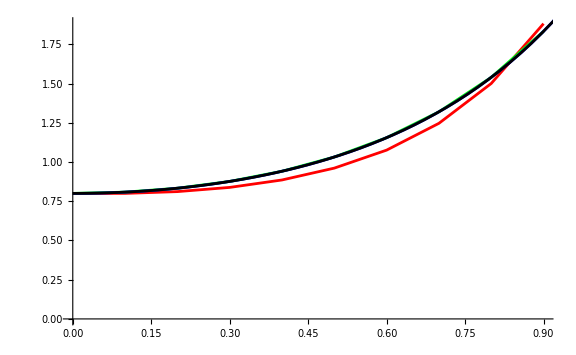

```mathematica
Show[Task1[f,y0,0.1]]
```

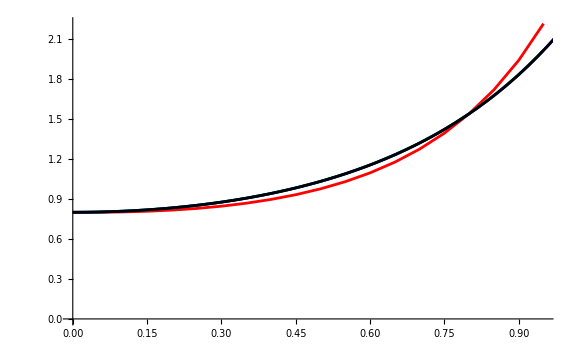

```mathematica
Show[Task1[f,y0,0.05]]
```

#### Вывод

Точность методов растёт от увеличения шага сетки.

### Задание 2

Решить задачу Коши для системы двух дифференциальных уравнений на отрезке :
	а) методом Эйлера с шагом  и , построить графики полученных решений;
	б) методом Рунге-Кутта 4-го порядка с шагом  и , построить графики полученных решений;
	в) с помощью функций DSolve и NDSolve, построить графики.
Сравнить все полученные решения.

Зададим функции, начальные условия и границы отрезков:

```mathematica
f1[x_,y_,z_]:=y+3z;
f2[x_,y_,z_]:=-y+5z;
y0=3;
z0=1;
```

#### Метод Эйлера

Зададим функцию для метода Эйлера:

```mathematica
Euler[f1_,f2_,a_,b_,y0_,z0_,h_]:=Module[{n,y,z,x,i},
n=(b-a)/h;
Array[y,0,n];
y[0]=y0;
Array[z,0,n];
z[0]=z0;
x[i_]:=a+i h;
For[i=0,i<n,i++,
y[i+1]=y[i]+h f1[x[i],y[i],z[i]];
z[i+1]=z[i]+h f2[x[i],y[i],z[i]];
];
{Table[{x[i],y[i]},{i,0,n-1}],Table[{x[i],z[i]},{i,0,n-1}]}
];
```

#### Метод Рунге-Кутта

Зададим функцию для метода Рунге-Кутта:

```mathematica
RungeKutta4Sys2[f1_,f2_,a_,b_,y0_,z0_,h_]:=Module[{n,y,z,x,i,k1,k2,k3,k4,r1,r2,r3,r4},
n=(b-a)/h;
Array[y,0,n];
y[0]=y0;
Array[z,0,n];
z[0]=z0;
x[i_]:=a+i h;
For[i=0,i<n,i++,
k1=h f1[x[i],y[i],z[i]];
r1=h f2[x[i],y[i],z[i]];
k2=h f1[x[i]+h/2,y[i]+k1/2,z[i]+r1/2];
r2=h f2[x[i]+h/2,y[i]+k1/2,z[i]+r1/2];
k3=h f1[x[i]+h/2,y[i]+k2/2,z[i]+r2/2];
r3=h f2[x[i]+h/2,y[i]+k2/2,z[i]+r2/2];
k4=h f1[x[i]+h,y[i]+k3,z[i]+r3];
r4=h f2[x[i]+h,y[i]+k3,z[i]+r3];
y[i+1]=y[i]+1/6(k1+2k2+2k3+k4);
z[i+1]=z[i]+1/6(r1+2r2+2r3+r4);
];
{Table[{x[i],y[i]},{i,0,n-1}],Table[{x[i],z[i]},{i,0,n-1}]}
];
```

Решим задачу Коши для данной системы дифференциальных уравнений и сравним полученные результаты:

```mathematica
Task2[f1_,f2_,y0_,z0_,h_]:=Module[{t1,t2,t3,t4,t5,gr1,gr2,gr3,gr4,y,z},
t1=Euler[f1,f2,a,b,y0,z0,h];
t2=RungeKutta4Sys2[f1,f2,a,b,y0,z0,h];
t3=DSolveValue[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==y0,z[0]==z0},{y[x],z[x]},x];
{t4,t5}=NDSolveValue[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[0]==y0,z[0]==z0},{y,z},{x,a,b}];
gr1=ListLinePlot[t1, ImageSize->Large, PlotStyle->Red];
gr2=ListLinePlot[t2, ImageSize->Large, PlotStyle->Green];
gr3=Plot[t3,{x,a,b}, ImageSize->Large, PlotStyle->Blue];
gr4=Plot[{t4[x],t5[x]},{x,a,b}, ImageSize->Large, PlotStyle->Black];
{gr1,gr2,gr3,gr4}
];
```

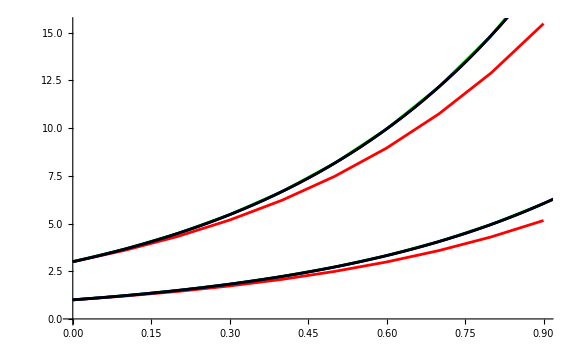

```mathematica
Show[Task2[f1,f2,y0,z0,0.1]]
```

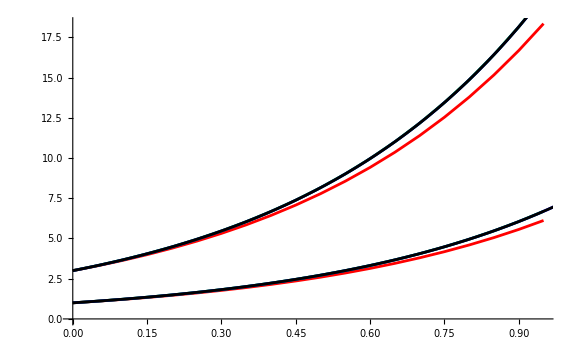

```mathematica
Show[Task2[f1,f2,y0,z0,0.05]]
```